```mathematica
xmin:=0;
xmax:=10;
ymin:=-1;
ymax:=4;
aspRat=(ymax-ymin)/(xmax-xmin);

fXY[x_,y_]:=2-E^(-(x/2-2)^2-(y-2)^2)+
	2E^(-(x/2-3)^2-(y/3-1)^2);
```

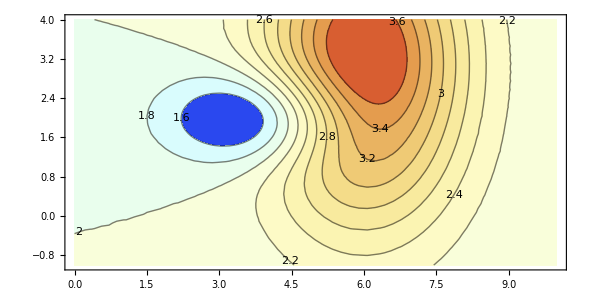

```mathematica
grf2Dd=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},
Contours->11,ContourLabels->All,
ColorFunction->"LightTemperatureMap",
BaseStyle->14,AspectRatio->aspRat,ImageSize->590]
(*plotrangePadding диапазон расположения графика *)
(*ContourPlot- контурный график на плоскости, показывает линии равного уровня*)
```

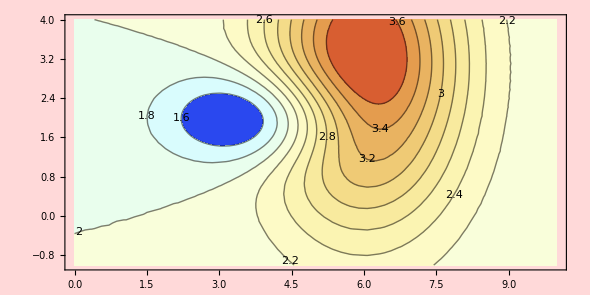

```mathematica
grf2Dc=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},
Contours->11,ContourLabels->All,
ColorFunction->"LightTemperatureMap",
BaseStyle->14,AspectRatio->aspRat,ImageSize->590,
PlotRegion->{{0.3,1},{0,0.8}},Background->LightRed]
 (*смещение графика*)
```

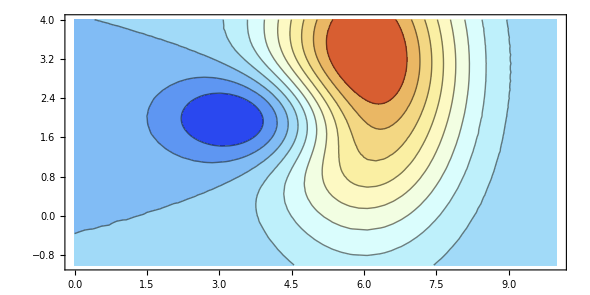

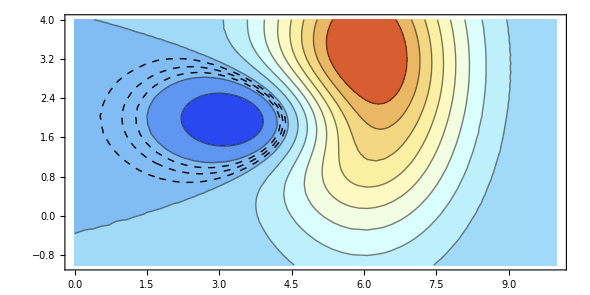

```mathematica
grf2D = ContourPlot[fXY[x, y], {x, xmin, xmax}, {y, ymin, ymax},
Contours->11, ContourLabels->None,
ColorFunction->"LightTemperatureMap", BaseStyle->14,
AspectRatio->aspRat, ImageSize->590]
grf2Dc=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},
Contours->{1.85,1.9,1.95},ContourStyle->Dashed, ContourShading-> None,
AspectRatio->aspRat,ImageSize->590];
Show[grf2D,grf2Dc]
```

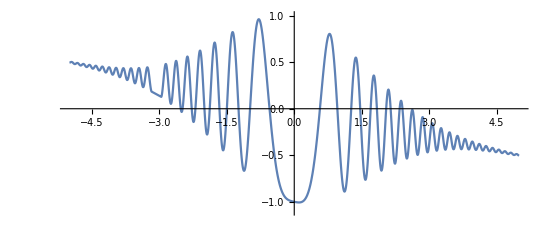

```mathematica
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x;
grf1DdFrgm=Plot[f3[x],{x,-4,-3},AspectRatio->3/7];
Plot[f3[x],{x,-5,5},AspectRatio->3/7,Epilog->
Inset[grf1DdFrgm,Scaled[{0.05,.05}],Scaled[{0,0}],4],
	PlotRange->{-1.1,1},PlotRangeClipping->False,ImageSize->550]
 (*репрезетует объект в виде графика*)
```

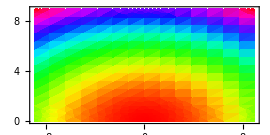
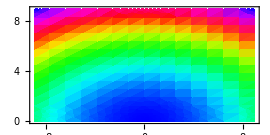

```mathematica
grf2Dd=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},
	BaseStyle->16,AspectRatio->1/2,
	PlotLegends->Placed[Automatic,Above],
	ColorFunction->Hue,ImageSize->270];
grf2De=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},
	BaseStyle->16,AspectRatio->1/2,
	PlotLegends->Placed[Automatic,Above],
	ColorFunction->(Hue[2/3-#]&),ImageSize->270];
Row[{grf2Dd,grf2De},Spacer[5]]
(*строит график плотности*)
```